# Vertical Clock Regulators for SXI

John Doty, Noqsi Aerospace ltd
April 6, 2010

This work is Copyright 2010 Noqsi Aerospace, Ltd.
This work is licensed under the Creative Commons Attribution - Share Alike 3.0 License.To view a copy of this license, visit http : // creativecommons.org/licenses/by - sa/3.0/or send a letter to Creative Commons, 171 Second Street, Suite 300, San Francisco, California, 94105, USA.

## A Mathematica notebook for investigating speed and stability of the SXI vertical clock regulators.

#### Introduction

CCD vertical clocks have high capacitances and often require large clock swings. This requires high drive current. The duty cycle is low, so the voltage regulators for the clock drivers need to behave well over a large dynamic range. If energy conservation is important, the idle current must be kept to a minimum. Loads are transient, and the driver voltages crosstalk with the video output through the substrate, so rapid recovery from transients is important.

This notebook contains an analysis stability and transient recovery characteristics of the vertical clock regulators for the ASTRO-H SXI instrument http://astro-h.isas.jaxa.jp/si/03_e.html.

#### Calculations

```mathematica
here = NotebookDirectory[];
```

First, the negative regulator. U1 is an LT1078. Q1 is a composite of an LM195 current/temperature limiter and an IRLR014 MOSFET. Rop, Cgd, and Cgs are parasitics. Cout and Rout are discrete components. The detailed schematic may be seen in the ParallelReg subsection of the main Driver Board design document. The simplified model schematic is:

```mathematica
Import[here<>"parlowmath.png"]
```

-Graphics-

Load the gEDAmath package. See www.noqsi.com/images/gEDAmath.nb.pdf for more details.

```mathematica
<<(here<>"gEDAmath.m")
```

This analysis needs some additional models.
Basic linear triode model.

```mathematica
fet[options___][refdes_]:=modeleqs[refdes,i["D"]==value(v["G"]-v["S"]),i["G"]==0,i["S"]+i["D"]==0]/.{options}/.{value->gm}
```

Current source model.

```mathematica
current[options___][refdes_]:={i[refdes,"1"]==value}/.{options}/.value->iin
```

Import the "netlist".

```mathematica
Clear[out]
<<(here<>"parlowmath.m")
```

in->out transfer function:

```mathematica
tf=Simplify[transferFunction[in,out]]/.stim->0
```

(2 bw π (1+cout rout s) (gm (-1+cgd rs s)+cgd s (1+cgs rs s)))/(2 bw π (1+cout rout s) (gm (-1+cgd rs s)+cgd s (1+cgs rs s))-s^2 (cout (1+gm rs+cgs (rop+rs) s)+cgd (1+cout rop s+cout rout s+gm (rs+cout rout rs s+rop (1+cout (rout+rs) s))+cgs s (rs+cout rout rs s+rop (1+cout (rout+rs) s)))))

Check for gain of 1 at DC.

```mathematica
tf/.s->0
```

1

Output impedance:

```mathematica
zf=Simplify[transferFunction[-stim,out]]/.in->0
```

-(s (1+cout rout s) (1+cgs rop s+cgs rs s+cgd rop s (1+cgs rs s)+gm (rs+cgd rop rs s)))/(2 bw π (1+cout rout s) (gm (-1+cgd rs s)+cgd s (1+cgs rs s))-s^2 (cout (1+gm rs+cgs (rop+rs) s)+cgd (1+cout rop s+cout rout s+gm (rs+cout rout rs s+rop (1+cout (rout+rs) s))+cgs s (rs+cout rout rs s+rop (1+cout (rout+rs) s)))))

Most of the analysis revolves about the denominator here, representing the "poles" or "natural frequencies" of the circuit. It is, however, useful to note that the numerator has a "zero" at -1/(cout rout). We'll see below that there's a pole near there, so there's "pole-zero cancellation" going on here. There's also a zero at the origin, so the output impedance approaches zero at DC:

```mathematica
zf/.s->0
```

0

First, go for a simple symbolic analysis, ignoring parasitics.

```mathematica
sympar={rop->0,cgs->0,cgd->0}
```

{rop→0,cgs→0,cgd→0}

```mathematica
zf/.sympar
```

-((1+gm rs) s (1+cout rout s))/(-cout (1+gm rs) s^2-2 bw gm π (1+cout rout s))

```mathematica
symf=Solve[Denominator[zf/.sympar]==0,s]
```

{{s→1/(cout+cout gm rs)(-bw cout gm π rout-√π √(-2 bw cout gm+bw^2 cout^2 gm^2 π rout^2-2 bw cout gm^2 rs))},{s→1/(cout+cout gm rs)(-bw cout gm π rout+√π √(-2 bw cout gm+bw^2 cout^2 gm^2 π rout^2-2 bw cout gm^2 rs))}}

As expected, two "natural frequencies". Of interest is the critical damping condition where they are equal: in a circuit like this, that's often a good place to be for speed and stability.

```mathematica
symcrit=Solve[{(s/.symf[[1]])==(s/.symf[[2]])},rout]
```

{{rout→-(√(2/π) √(1+gm rs))/(√bw √cout √gm)},{rout→(√(2/π) √(1+gm rs))/(√bw √cout √gm)}}

Now move into the numeric domain.

Units are MHz, nF, kΩ, μs, mS.

bw->0.2 MHz		Opamp gain-bandwidthproduct
rop->1.0 kΩ		Opamp open loop output resistance
cgs->0.265 nF		FET gate-source capacitance
cout->22000		Use 22 μF

```mathematica
devpar={bw->0.2,rop->1.0,cgs->0.265,cout->2*470,rs->0.01}
```

{bw→0.2,rop→1.,cgs→0.265,cout→940,rs→0.01}

Measured transconductance of the composite FET is 2000 mS  at 1 A. For the high current case, assume 0.1 A. The LM195 is active, reducing the effective Cgd.

```mathematica
hicurr={gm->2000Sqrt[0.1],cgd->0.02}
```

{gm→632.456,cgd→0.02}

For low current, 1 mA, the LM195 is inactive, so raise Cgd to 50 pF.

```mathematica
locurr={gm->2000Sqrt[0.001],cgd->0.05}
```

{gm→63.2456,cgd→0.05}

```mathematica
symcrit[[2]]/.devpar/.hicurr
symcrit[[2]]/.devpar/.locurr
```

{rout→0.00626234}

{rout→0.00934904}

Given lists of parameters, extract "natural frequencies".

```mathematica
natfreqs[p___]:=s/.Solve[Denominator[zf/.devpar/.Flatten[{p}]]==0,s]
```

Stability index: range is -1 to 1. 1 is the most stable. Negative numbers are unstable. As a rough rule of thumb, I like to see numbers >0.5 here.

```mathematica
stability[z_]:=-Re[z]/Abs[z]
SetAttributes[stability,Listable]
```

Start with Rout near the critical point identified above.

```mathematica
natfreqs[hicurr,rout->0.01]
```

{-5075.16,-12.3902,-1.05674,-0.119438}

How do we interpret this? The first solution is far outside our bandwidth, and may be ignored. It's only telling us that we cannot in practice separate the effects of Cgs and Cgd. The last is approximately -1/(cout rout), representing recharge of Cout at approximately constant voltage. This suggests that the output voltage will recover quickly to a transient, so the recovery of Cout's charge is simply controlled by Rout. Another way to say this is that the zero at -1/(cout rout), noted above, cancels this pole. We will therefore largely ignore it.

```mathematica
stability[%]
```

{1.,1.,1.,1.}

Stability is good. Now try the low current case.

```mathematica
natfreqs[locurr,rout->0.01]
```

{-1429.01,-3.75387,-0.387824,-0.152599}

```mathematica
stability[%]
```

{1.,1.,1.,1.}

Slower (look at the third natural frequency), but stable. It's to be expected that the circuit slows down as it settles into the low current case.

We can take the third natural frequency as an indicator of the speed. The interesting case for speed is the high current case, because the current will only be low if the circuit is already near equilibrium.

```mathematica
speed[r_]:=-Re[natfreqs[hicurr,rout->r]][[3]]
```

For stability, we're interested in every natural frequency in both high and low current cases. Any instability will be trouble.

```mathematica
stab[r_]:=Min@@Flatten[{stability[natfreqs[hicurr,rout->r]],stability[natfreqs[locurr,rout->r]]}]
```

Investigate speed and stability as a function of Rout.

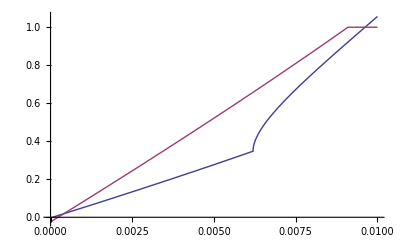

```mathematica
Plot[{speed[r],stab[r]},{r,0,0.01}]
```

The model with parasitics is telling us pretty much the same story as the simpler analysis. The optimum Rout is near ~1.3Ω.

Plot the response to a change in load using the stepResponse function from the gEDAmath package. Its numerical inverse Laplace transform adds an unknown constant of integration, so take a sample from late in the curve to be the baseline.

```mathematica
pstep[tf_,d_]:=With[{sr=stepResponse[tf,2d,d/1000]},Plot[Evaluate[sr-(sr/.t->d)],{t,0,d},PlotRange->All]]
```

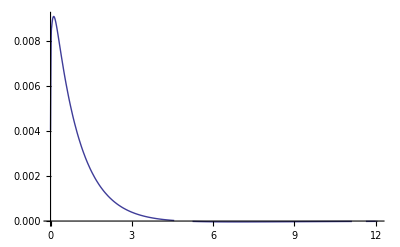

```mathematica
pstep[zf/.devpar/.hicurr/.rout->0.01,16]
```

```mathematica
natfreqs[hicurr,rout->0.01]
```

{-5075.16,-12.3902,-1.05674,-0.119438}

```mathematica
stability[%]
```

{1.,1.,1.,1.}

Give the positive regulator the same treatment.

```mathematica
Import[here<>"parhimath.png"]
```

-Graphics-

Import the "netlist".

```mathematica
Clear[out]
<<(here<>"parhimath.m")
```

```mathematica
tf=Simplify[transferFunction[in,out]]/.stim->0
```

(2 bw π (gm+cgs s) (1+cout rout s))/(2 bw π (gm+cgs s) (1+cout rout s)+s (gm (1+cgd rop s) (1+cout rout s)+s (cout+cgd cout rop s+cgs (1+cout (rop+rout) s+cgd rop s (1+cout rout s)))))

Check for gain of 1 at DC.

```mathematica
tf/.s->0
```

1

Output impedance:

```mathematica
zf=Simplify[transferFunction[-stim,out]]/.in->0
```

(s (1+cgd rop s+cgs rop s) (1+cout rout s))/(2 bw π (gm+cgs s) (1+cout rout s)+s (gm (1+cgd rop s) (1+cout rout s)+s (cout+cgd cout rop s+cgs (1+cout (rop+rout) s+cgd rop s (1+cout rout s)))))

Output impedance approaches zero at DC:

```mathematica
zf/.s->0
```

0

```mathematica
devpar={bw->0.2,rop->1.0,cgs->0.265,cout->2*470}
```

{bw→0.2,rop→1.,cgs→0.265,cout→940}

First, go for a simple symbolic analysis, ignoring parasitics.

```mathematica
sympar={rop->0,cgs->0,cgd->0}
```

{rop→0,cgs→0,cgd→0}

```mathematica
zf/.sympar
```

(s (1+cout rout s))/(2 bw gm π (1+cout rout s)+s (cout s+gm (1+cout rout s)))

Once again, zeros at the origin and -1/(cout rout).  The same pole-zero cancellation seen above will occur here.

```mathematica
symf=Solve[Denominator[zf/.sympar]==0,s]
```

{{s→(-gm-2 bw cout gm π rout-√(-8 bw gm π (cout+cout gm rout)+(gm+2 bw cout gm π rout)^2))/(2 (cout+cout gm rout))},{s→(-gm-2 bw cout gm π rout+√(-8 bw gm π (cout+cout gm rout)+(gm+2 bw cout gm π rout)^2))/(2 (cout+cout gm rout))}}

```mathematica
symcrit=Solve[(s/.symf[[1]])==(s/.symf[[2]]),rout]
```

{{rout→(√gm-2 √bw √cout √(2 π))/(2 bw cout √gm π)},{rout→(√gm+2 √bw √cout √(2 π))/(2 bw cout √gm π)}}

```mathematica
symcrit[[2]]/.devpar/.hicurr
symcrit[[2]]/.devpar/.locurr
```

{rout→0.00316048}

{rout→0.00816379}

Very similar numbers to the negative regulator.

```mathematica
natfreqs[hicurr,rout->0.003]
```

{-20352.5,-7.8352,-0.651272,-0.512018}

```mathematica
natfreqs[locurr,rout->0.003]
```

{-8179.87,-3.42023,-0.12649-0.245006 ⅈ,-0.12649+0.245006 ⅈ}

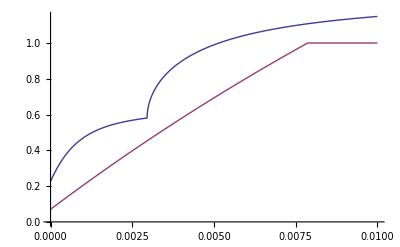

```mathematica
Plot[{speed[r],stab[r]},{r,0,0.01}]
```

This makes it appear that it's speedier to have high Rout, but it's a little misleading. With Rout of 10Ω, a load change makes a big voltage transient because Cout can't contribute much current:

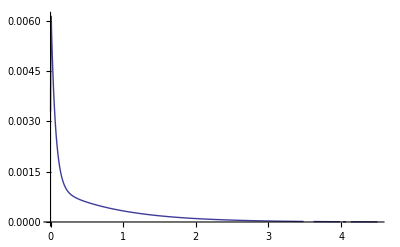

```mathematica
hir=pstep[zf/.devpar/.hicurr/.rout->0.01,5]
```

With Rout of 4.7Ω, the transient is smaller:

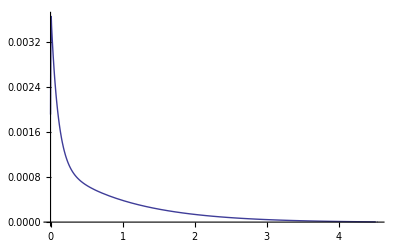

```mathematica
lor=pstep[zf/.devpar/.hicurr/.rout->0.0047,5]
```

Comparing the two, the settling tails are almost the same, so the lower resistance is better.

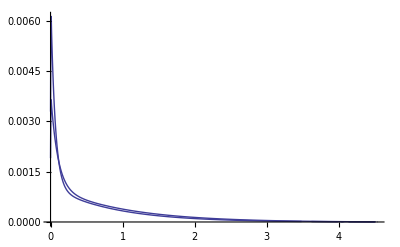

```mathematica
Show[hir,lor]
```

#### Conclusions

The SXI vertical clock rate is 32 kHz, so output settling in a few microseconds represents excellent performance. The fact that the lowest frequency pole is approximately cancelled by a zero indicates that the circuit itself takes longer to settle than its output does. This means that the circuit is moderating the current surges from the power rails on clock transitions, a good thing for it to do. The components need little idle current, so these circuits are reasonably efficient.

I think this notebook demonstrates the power of a mixture of symbolic and numerical linear circuit analysis. The symbolic analysis yields insights difficult to perceive in a purely numerical environment like SPICE, and also leads to very fast and comprehensible linear numerical models.